```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GitHub/NMRProcess2"}]];
```

```mathematica
<<"NMRProcess2`"
```

NMR Processing
Version 2.0.0 Fri 25 Mar 2016 20:27:32
(c)2016 Marcel Utz
marcel.utz@southampton.ac.uk

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/mu3q/GitHub/NMRprocess2/Examples

```mathematica
rawfid=ReadVarian["../ExampleData/db2m_1mM_13chsqc2.fid/fid"]
```

Reading 200 blocks of 800 complex points; data type: Integer32

-|NMR..1--

```mathematica
fid=SetProp[SetTimeDomain[rawfid,{800,100}],
		{Offset->{4.76,40.},SpectralWidth->{14.,80.}}]
```

-|NMR..2--

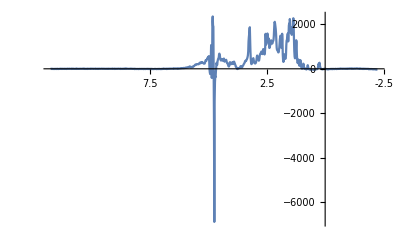

```mathematica
PlotNMR1D[FFT1D[ExtractTransient[fid,{1}],Phase0->90,Phase1->0,LeftShift->0],PlotRange->All]
```

```mathematica
spect=StatesFFT2[fid,LeftShift->0,Phase2->90.,Phase1->0.,SI1->256,SI2->2048,T1Dir->-1,T1Shift->True]
```

-|NMR..2--

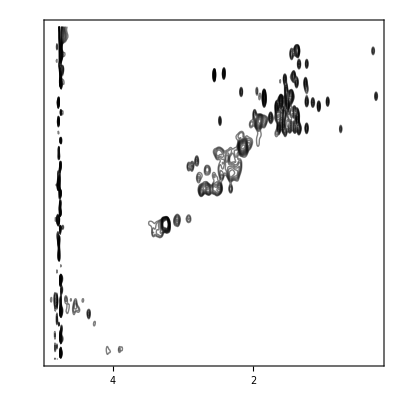

```mathematica
NMRContourPlot[Crop[spect,{{8.0,-.5},{72.0,5.0}}],Gain->2]
```